# 3) Planar 3-R Manipulator

Setting notebook directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Including package ‘planar2R_utils’

```mathematica
<< "planar2R_utils.m";
```

## (a) Forward kinematics for the planar 3-R serial manipulator

→ Implementation of “fwdKin3RSpatial” function to solve forward kinematics equations for a planar 3R serial manipulator.

→ Position of the base of the manipulator = {x0, y0,}

```mathematica
fwdKin3RSpatial[{x0_,y0_},{l1_,l2_,l3_},{θ1_,θ2_,θ3_} ,{x_,y_,phi_}] :=
Module[{sol},
			sol = {x -> x0 + l1 Cos[θ1] + l2 Cos[θ1+θ2]+l3 Cos[θ1+θ2+θ3],
	  y -> y0 + l1 Sin[θ1] + l2 Sin[θ1+θ2]+l3 Sin[θ1+θ2+θ3],
	  phi ->  θ1+θ2+θ3};
Return[N[sol]];
];
```

## (b) Inverse kinematics for the planar 3-R serial manipulator

Implementation of “invKin3RSpatial” function to solve forward kinematics equations for a spatial 3R serial manipulator.

```mathematica
invKin3RSpatial[{x0_,y0_},{l1_,l2_,l3_},{x_,y_,phi_},{θ1_,θ2_,θ3_},{solθ1,solθ2}] :=
(* p̄ = {x,y} is the given position of the tip and (phi) is the orientation of the 3rd link w.r.t base axis, phi = θ1+θ2+θ3 *)
Module[{d,p,P,θ12,X,Y,θ1var,θ2var,θ3var,solθ1var,solθ2var,a,b,c},
p = {x,y};
d = Norm[p-{x0,y0}];
(*--------------------------------------------------*)
(* To check if the end effector point is within the workspace *)

(*
If[NumericQ[l1] && NumericQ[l2] && NumericQ[l3] && Map[negativeQ, (l2 + l3) - d || (d-Abs[l2-l3])],
   
Print["invKin3RSpatial::error: The points x= ",    x,", y= ",y," and z= ",z, " are beyond the workspace of the spatial 3R serial manipulator!"];
Return[{{}}];	
]; 
*)

(*--------------------------------------------------*)
(* To check if l1, l2 and l3 are non-zero positive numbers *)

If[NumericQ[l1] && NumericQ[l2] && NumericQ[l3] && ((Map[negativeQ,l1 || l2|| l3])||Map[zeroQ, l1||l2||l3]), Print["invKin3RSpatial::error: The link lengths should be positive, whereas l1=",l1," l2=",l2," and l3=",l3,""];
	Return[{{}}];
	];
(*--------------------------------------------------*)
(* Converting the planar 3R manipulator problem to a 2R planar serial manipulator problem in links-1 and links-2 *)
(*--------------------------------------------------*)
X = x - l3 Cos[phi]; 
Y = y - l3 Sin[phi];
P = {X,Y};
a = 2X l2;
b = 2 Y l2;
c = l1^2-l2^2-X^2-Y^2;
(*--------------------------------------------------*)
(* Checking the case where a = 0 and b = 0 i.e. the joint between links 2 and 3 is at origin, which means l1 = l2*)
If[Map[zeroQ,a &&b&&(l1-l2)],Print["Multiple solutions for θ1"];
Return[{{θ1 -> Interval[{0,2Pi}],θ2->Pi}}]];
(*--------------------------------------------------*)
(* Solution 1 *)

θ12 = ArcCos[-c/(√(a^2+b^2))] + ArcTan[a,b];
θ1var = ArcTan[(X-l2 Cos[θ12])/l1,(Y-l2 Sin[θ12])/l1];
θ2var = θ12 - θ1var;
θ3var = phi - θ12;

solθ1var = {θ1 -> θ1var,θ2->θ2var,θ3->θ3var};
(*--------------------------------------------------*)
(* Solution 2 *)

θ12 = -ArcCos[-c/(√(a^2+b^2))] + ArcTan[a,b];
θ1var = ArcTan[(X-l2 Cos[θ12])/l1,(Y-l2 Sin[θ12])/l1];
θ2var = θ12 - θ1var;
θ3var = phi - θ12;

solθ2var = {θ1 -> θ1var,θ2->θ2var,θ3->θ3var};

(*--------------------------------------------------*)
solθ = {solθ1->solθ1var,solθ2->solθ2var};
Return[solθ];
];
```

## (c) Validation of Results of Forward and Inverse Kinematic solutions for the given lengths l1 = 1, l2 = 1/2, l3 =1/4

```mathematica
Knownvar = {l1 ->1,
l2 -> 1,
l3 -> 1,x0->0,y0->0};
```

## (i) Creating a random input vector

```mathematica
(* Creating a random input vector θ^* = {Subscript[θ, 1]^*,Subscript[θ, 2]^*,Subscript[θ, 3]^*} *)
(* Also, Subscript[θ, i]^* ∈ [0,2π], i =1,2,3, are random numbers *)
θstar= RandomReal[{0,2π},3]
θstar1 = {Pi/4,Pi,-Pi/4};
```

{4.5227,0.62313,3.45136}

## (ii) Forward Kinematics Analysis with "θ1"

```mathematica
(* Getting the random vector θ^* from randvec module *)
(*{θ1r,θ2r,θ3r} = θ1; *)
(* Using the module fwdKin3RSpatial to find the tip point along with the phi value*)
p1 = fwdKin3RSpatial[{x0,y0},{l1,l2,l3},θstar1,{x,y,phi}]/.Knownvar
```

{x→-1.,y→0.,phi→3.14159}

## (iii) Inverse Kinematics for output "p1"

```mathematica
(* Getting solutions in θ for p^* as the tip point using inverse kinematics analysis *)
θsol =invKin3RSpatial[{x0,y0},{l1,l2,l3},{x,y,phi}/.p1,{θ1,θ2,θ3},{solθ1,solθ2}]/.Knownvar;
(* θsol has two possible configurations  *)
(* The possible solutions given by θsol will either both be 
real(when p^(*1) is within the workspace of the 3R planar manipulator) or both be complex (when p^* is outside the workspace of the 3R spatial manipulator)) *)
(* --------------------------------------------------*)
θsol1 = θsol[[1]]  (* 1st solution *)
θsol2 = θsol[[2]]  (* 2nd solution *)
(* --------------------------------------------------*)
```

solθ1→{θ1→-3.14159,θ2→3.14159,θ3→3.14159}

solθ2→{θ1→0.,θ2→-3.14159,θ3→6.28319}

## (d) Forward Kinematics and Inverse Kinematics analysis for l1 = 1, l2 = 1/2, l3 =1/4 and θ = [π/6,π/4,π/3]^T

## Forward Kinematics Analysis

```mathematica
Knownvar2 = {l1->1,l2->1/2,l3->1/4,x0 ->0,y0 ->0};
```

```mathematica
θstar2 = {Pi/6,Pi/4,Pi/3};
p2 = fwdKin3RSpatial[{x0,y0},{l1,l2,l3},θstar2,{x,y,phi}]/.Knownvar2
```

{x→0.818658,y→1.15974,phi→2.35619}

## Inverse Kinematics Analysis for the point we get from Forward Kinematics analysis

```mathematica
θ2sol =invKin3RSpatial[{x0,y0},{l1,l2,l3},{x,y,phi}/.p2,{θ1,θ2,θ3},{solθ1,solθ2}]/.Knownvar2;
```

```mathematica
(* θsol has two possible configurations  *)
(* The possible solutions given by θsol will either both be 
real(when p2 is within the workspace of the 3R planar manipulator) or both be complex (when p^* is outside the workspace of the 3R spatial manipulator)) *)
(* --------------------------------------------------*)
θ2sol1 = θ2sol[[1]]  (* 1st solution *)
θ2sol2 = θ2sol[[2]]  (* 2nd solution *)
(* --------------------------------------------------*)
```

solθ1→{θ1→0.523599,θ2→0.785398,θ3→1.0472}

solθ2→{θ1→1.03459,θ2→-0.785398,θ3→2.107}

Thus, solθ1 (one of the two solutions) gives us the same initial theta vector θ = [π/6,π/4,π/3]^T we considered (i . e .) after obtaining the end - effector tip point’ s coordinates using Forward Kinematics Analysis and then using the point to obtain solθ1 by doing Inverse Kinematic Analysis.

```mathematica
(* Define the end points of the links for both the configurations of the manipulator. *)
{θ1,θ2,θ3} = {θ1,θ2,θ3}/.θ2sol1[[2]];

p1a= {x0,y0}+l1*{Cos[θ1],Sin[θ1]}/.Knownvar2;
p2a = p1a + l2 *{Cos[θ1+θ2], Sin[θ1+θ2]}/.Knownvar2;
p3a = p2a + l3 *{Cos[θ1+θ2+θ3], Sin[θ1+θ2+θ3]}/.Knownvar2;

{θ1,θ2,θ3} = {θ1,θ2,θ3}/.θ2sol2[[2]];
p1b= {x0,y0}+l1*{Cos[θ1],Sin[θ1]}/.Knownvar2;
p2b = p1b + l2 *{Cos[θ1+θ2], Sin[θ1+θ2]}/.Knownvar2;
p3b = p2a + l3 *{Cos[θ1+θ2+θ3], Sin[θ1+θ2+θ3]}/.Knownvar2;
```

## Plotting both the manipulator configurations obtained from Inverse Kinematics

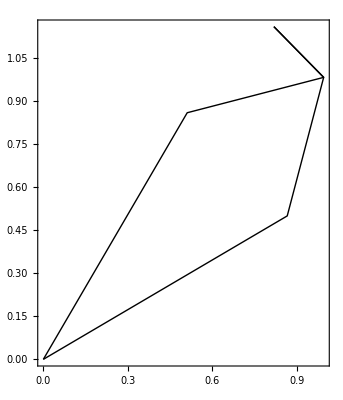

```mathematica
(* Plotting both the configurations of the manipulator *)

Show[Graphics[Line[{{x0,y0},p1a,p2a,p3a}],Frame -> True]/.Knownvar2,Graphics[Line[{{x0,y0},p1b,p2b,p3b}],Frame -> True]/.Knownvar2]
```

## (e) Singularity Conditions for 3R planar Manipulator

Using the Inverse Kinematic Analysis, we can find the workspace boundaries for the planar 3-R manipulator.

When we do Inverse Kinematic Analysis of a Planar 3-R manipulator, we have {x, y, Φ} as our input space and { θ1, θ2 } as output space. 
→ This means that the orientation of the third link if fixed w.r.t to the reference basis vectors. 
Hence, the singularity conditions for the entire planar 3-R manipulator can be found by solving for the workspace boundaries of the effective 2-R planar manipulator with links 1 and 2. 

→ For a 2-R planar serial manipulator with links 1 and links2 the singularity conditions are the configurations, where, 
	
1) Link1 and Link2 are completely stretched out in a straight line so that Link2 can only move tangentially and has a single degree of freedom at that point. 

Here, 
					θ1 = [0, 2π] and θ2 = 0

2) Link2 wraps up on Link1 such that, 

					θ1 = [0, 2π] and θ2 = π

## (f) Workspace Boundaries for 3R planar Manipulator

Workspace boundaries can be constructed by solving the effective 2R planar manipulator problem and then using the singularity conditions to derive the equations for the workspace boundaries for the 3R planar manipulator. The workspace boundaries in this case are function of the angle ϕ since Inverse Kinematic analysis requires this as an input and also because for a given ϕ, the orientation of the third link doesn’t change.

Thus, we obtain,
			
→ Outer workspace boundary Ξ  
			(x-l3 cos(ϕ) )^2 + (y-l3 sin(ϕ) )^2 =  (l1+l2 )^2
						   
						   and 

→ Inner workspace boundary	 Ξ 
			(x-l3 cos(ϕ) )^2 + (y-l3 sin(ϕ) )^2 =  (l1-l2 )^2	
			
								where l1,l2,l3 ∈ R^+
			
The above equations are circle equations with centre at the joint between link2 and link3 because this indeed supports the equations governing the workspace boundaries of a 2R planar manipulator.

## (g) Area of the Workspace for a given set of link lengths

From the workspace boundaries obtained in the previous question, we can find the area of workspace for given [l1, l2, l3].

Area of Workspace in the 3R planar manipulator case as it is in the 2R planar manipulator case with links 1 and 2, except for the fact that the values of l3 and ϕ shift the centre of the circle from (0,0) to (l3 cos(ϕ),l3 sin(ϕ)) instead. 

Area of Workspace of 3R planar = π ( (l1+l2)^2 - (l1-l2)^2)
						    = 4π l1 l2

## (h) Link lengths that maximise the area of the workspace

Area of the workspace depends on l1 and l2, and only the coordinates of the center of the workspace boundary depends on the value of l3.

Hence, to maximise the workspace area, we need to set l3 = 0, so that 
					a = l1 + l2 + 0 = l1 + l2 
					a = l1 + l2 
To find the optimal l1 and l2 that maximise the workspace area, we can consider 
					l2 = (a - l1)
Now, area becomes,
					Area = 4π (l1) (a - l1)
					Area	= 4π (a l1 - l1^2)
Area is maximised, when 
					(d(Area))/(d(l1)) = 0
This gives us that, 	
					l1 = a/2	
Hence, from  a = l1 + l2, we get that, 
					l2 = a/2
					
Therefore the link lengths that maximise the area of the workspace are 
				l1 = a/2,  l2 = a/2 and l3 = 0